```mathematica
SetDirectory[NotebookDirectory[]];
Clear["Global`*"];
```

```mathematica
Input data;
```

```mathematica
A = 1.0*Import["../data/fem_output/matrixPressure.txt","Data"];
B = 1.0*Import["../data/fem_output/rightPart.txt","Data"];
resGauss = 1.0*Flatten[Import["../data/gauss_output/a_solution.txt","Data"]];
systemNum=Import["../data/fem_input/initial_conditions/systemNum.json","RawJSON"][[1]];
matrixSize =Import["../data/fem_input/initial_conditions/systemParameters.json","RawJSON"][[1]][[systemNum+1]][[1]];
borderLength =1.0*Import["../data/fem_input/initial_conditions/systemParameters.json","RawJSON"][[1]][[systemNum+1]][[14]];
method = Import["../data/fem_input/initial_conditions/systemParameters.json","RawJSON"][[1]][[systemNum+1]][[13]];
```

```mathematica
Diagram of pressure;
```

```mathematica
xOrigin = 0.0;hx =borderLength/ (matrixSize-1);
yOrigin = 0.0;hy =borderLength / (matrixSize-1);

matrixResultGauss = Table[0,{i,1,matrixSize},{j,1,matrixSize}];
diagram3DGauss= Table[{0,0,0},{i,1,matrixSize},{j,1,matrixSize}];
If[method≠ "rect2",{(*non rectangle second order*)For[i=1,i≤ matrixSize,i++,
{For[j=1,j≤ matrixSize,j++,{
diagram3DGauss[[i]][[j]][[1]]=xOrigin + hx *( i-1);
diagram3DGauss[[i]][[j]][[2]]=yOrigin + 2*hy * (j - 1);}]}]},
{
(*rectangle second order*)
For[i=1,i≤ matrixSize,i++,{
If[Mod[i,2]==0,{For[j=1,j≤ matrixSize-(matrixSize-1)/2,j++,
diagram3DGauss[[i]][[j]][[1]]=xOrigin + hx *( i-1);
diagram3DGauss[[i]][[j]][[2]]=yOrigin +2* hy * (j - 1);
];
For[j=1,j≤ (matrixSize-1)/2,j++,diagram3DGauss[[i]]=Delete[diagram3DGauss[[i]],-1];];
},{For[j=1,j≤ matrixSize,j++,{
diagram3DGauss[[i]][[j]][[1]]=xOrigin + hx *( i-1);
diagram3DGauss[[i]][[j]][[2]]=yOrigin + hy * (j - 1);
}]
}]
}];
}];

l=1;
For[i=1,i≤ matrixSize,i++,
k=1;
While[k≤ Length[diagram3DGauss[[i]]], 
diagram3DGauss[[i]][[k]][[3]]=resGauss[[l]];
k++;
l++;]]
```

```mathematica
(*3d graph*)
listPlotDiagram = ListPointPlot3D[diagram3DGauss,
PlotStyle->PointSize[0.02],
ViewPoint->{-0.790,3.054,0.947},
PlotRange->All,
AxesLabel->{Style["z",16,
Black,Italic,FontFamily->"Times"],
Style["s",16,Italic,Black,FontFamily->"Times"],
Style["P",16,Black,Italic,FontFamily->"Times"]
},
AxesStyle->Directive[Black,14,Arrowheads[{0.0,0.03}],FontFamily->"Times"],
AxesStyle->Thick,
ImageSize->500,
Lighting->{{"Ambient", LightBlue}}];
(*axes labels for simple search rotation*)
axesOrigin1 = Graphics3D[{PointSize[0.05],
Point[{0,0,0},VertexColors->Red]}];
axesOrigin2 = Graphics3D[{PointSize[0.05],
Point[{0.02,0,0},VertexColors->Blue]}];
axesOrigin3 = Graphics3D[{PointSize[0.05],
Point[{0,0.02,0},VertexColors->Green]}];
Show[listPlotDiagram]
```

-Graphics3D-

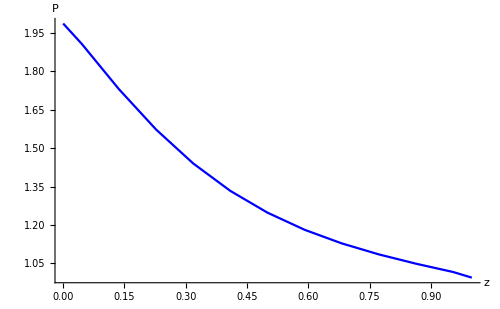

```mathematica
Proection;
proectionValues = Table[{0,0},{i,1,matrixSize}];

For[i=1,i≤matrixSize,i++,{
column =If[Mod[Length[diagram3DGauss[[i]]],2]==0,Length[diagram3DGauss[[i]]]/2,(Length[diagram3DGauss[[i]]]+1)/2];
proectionValues[[i]][[1]]=diagram3DGauss[[i]][[column]][[1]];
proectionValues[[i]][[2]]=diagram3DGauss[[i]][[column]][[3]];
}];


proection = ListLinePlot[proectionValues,
PlotRange->All,
GridLines->Full,
ImageSize->500,
PlotStyle->{Blue},
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],Style["P",16,Italic,Black,FontFamily->"Times"]},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
PlotStyle->{Darker[Red,0.4],Thick}];


Show[proection,PlotRange->All]
```

```mathematica
Surface;
surface=Plot3D[1.0+0.2*s,{z,0.0,borderLength},{s,0.0,borderLength},
AxesLabel->{Style["z",16,Black,Italic,FontFamily->"Times"],
Style["s",16,Italic,Black,FontFamily->"Times"]
},
AxesStyle->Directive[Black,14,FontFamily->"Times"],
AxesStyle->Thick,
Background->White,
BoundaryStyle->Thick,
Filling->Bottom,
ImageSize->500,
FillingStyle-> LightBlue,
Lighting->{{"Ambient", LightBlue}}, ViewPoint->{3.07559,0.7744956,0.888102}];
Show[surface]
```

-Graphics3D-

```mathematica
Comparision of solutions;
```

```mathematica
solution1 = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
solution2 = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
solution3 = 1.0*Flatten[Import["../data/gauss_output/solution.txt","Data"]];
```

```mathematica
Norm[solution1-solution2,Infinity]
```

0.

```mathematica
Norm[solution2-solution3,Infinity]
```

0.

```mathematica
Norm[solution1-solution3,Infinity]
```

0.

```mathematica
(0.02^(2/3)*0.0005)/0.0002
```

0.184202

```mathematica
Solve[x*0.001==0.015,x]
```

{{x→15.}}

```mathematica
Solve[15==x/0.0002,x]
```

{{x→0.003}}

```mathematica
(0.00018-0.0002)/0.02
```

-0.001

```mathematica
Sinh[50.0]
```

2.59235×10^21